```mathematica
Clear[DD];
```

```mathematica
model ={S'[t]== -β II[t]S[t]/(S[t]+II[t]+R[t]+DDD[t]),II'[t]== β II[t]S[t]/(S[t]+II[t]+R[t]+DDD[t]) - γ II[t] - μ II[t],R'[t]== γ II[t],DDD'[t] == μ II[t]}
```

{S'(t)==-(β II(t) S(t))/(DDD(t)+II(t)+R(t)+S(t)),II'(t)==(β II(t) S(t))/(DDD(t)+II(t)+R(t)+S(t))-γ II(t)-μ II(t),R'(t)==γ II(t),DDD'(t)==μ II(t)}

```mathematica
ic={S[0]==998,II[0]==1,R[0]== 1,DDD[0]==0}
```

{S(0)==998,II(0)==1,R(0)==1,DDD(0)==0}

```mathematica
Clear[β,γ,μ]
params = {β->.09,γ-> .01,μ ->  .002}
```

{β→0.09,γ→0.01,μ→0.002}

```mathematica
(* sol = NDSolve[{model /.β -> 1 /. γ-> .5 ,ic},{S,II,R},{t,0,100}];*)
sol = NDSolve[{model /. params,ic},{S,II,R,DDD},{t,0,1000}];
```

```mathematica
sol
```

{{S→InterpolatingFunction[…],II→InterpolatingFunction[…],R→InterpolatingFunction[…],DDD→InterpolatingFunction[…]}}

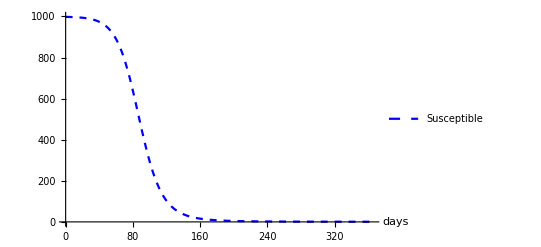

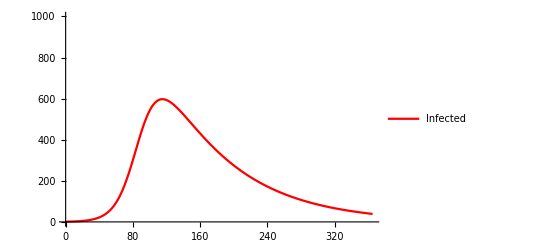

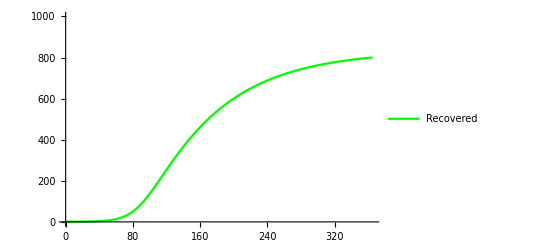

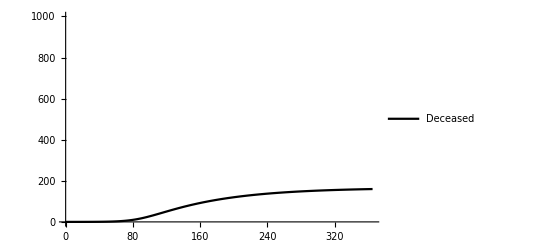

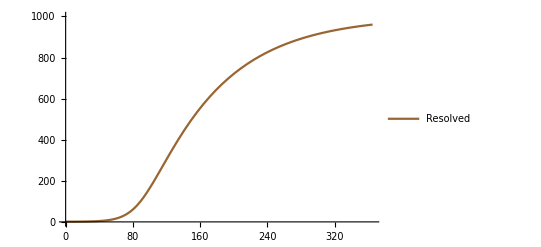

```mathematica
Susc =Plot[S[t]/. sol,{t,0,365},PlotStyle->{Blue,Thick,Dashed},LabelStyle-> {Large},PlotRange-> {0,1000},PlotLegends->{"Susceptible"},AxesLabel-> {"days",""}]
Infect =Plot[II[t]/. sol,{t,0,365},PlotStyle->{Red,Thick},LabelStyle-> {Large},PlotRange-> {0,1000},PlotLegends->{"Infected"}]
Recov =Plot[R[t]/. sol,{t,0,365},PlotStyle->{Green,Thick},LabelStyle-> {Large},PlotRange-> {0,1000},PlotLegends->{"Recovered"}]
Deceased =Plot[DDD[t]/. sol,{t,0,365},PlotStyle->{Black,Thick},LabelStyle-> {Large},PlotRange-> {0,1000},PlotLegends->{"Deceased"}]
Resolved =Plot[DDD[t]+R[t]/. sol,{t,0,365},PlotStyle->{Brown,Thick},LabelStyle-> {Large},PlotRange-> {0,1000},PlotLegends->{"Resolved"}]
```

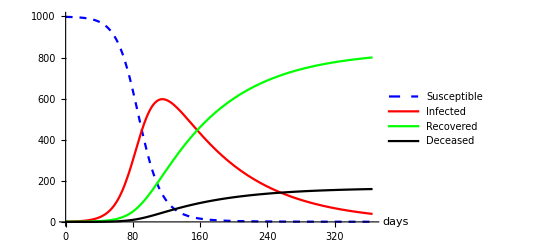

```mathematica
Show[{Susc,Infect,Recov,Deceased}]
```